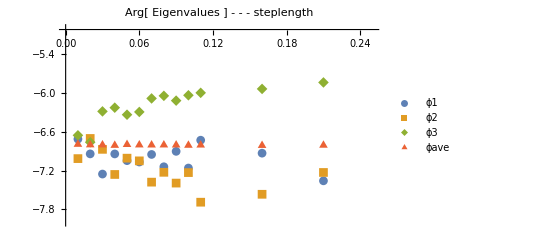

```mathematica
(*
running in the cluster:ne=4, 1000 50000 30 1;
newsteplength: ne=, 1000 50000 50 1, steplength from 0.03->0, by 0.005,
newi1, ne=4. newi2, ne=10. newi3, ne=4, nMea=100000, from 0.005->0, by 0.001.

*)
bm=Import["Google Drive/jie_programs/QHlattice/steplength/teststeplength","Table"];
n:=Length[bm]
x=Table[bm[[i]][[1]],{i,1,n,1}];
phase1= Table[{x[[i]],bm[[i]][[2]]},{i,1,n}];
phase2= Table[{x[[i]],bm[[i]][[3]]},{i,1,n}];
phase3= Table[{x[[i]],bm[[i]][[4]]},{i,1,n}];
ave=Table[(bm[[i]][[2]]+bm[[i]][[3]]+bm[[i]][[4]])/3,{i,n}];
phaseave= Table[{x[[i]],ave[[i]]},{i,1,n}];
ϕ1dif= Table[{x[[i]],bm[[i]][[2]]-ave[[i]]},{i,1,n}];
ϕ2dif= Table[{x[[i]],bm[[i]][[3]]-ave[[i]]},{i,1,n}];
ϕ3dif= Table[{x[[i]],bm[[i]][[4]]-ave[[i]]},{i,1,n}];


ListPlot[{phase1,phase2,phase3,phaseave},PlotLegends->{"ϕ1","ϕ2", "ϕ3","ϕave"},PlotMarkers->Automatic, PlotLabel->"Arg[ Eigenvalues ] - - - steplength",PlotRange->{{0,0.25},{-8,-5}}]
```

```mathematica
bm1=Import["Google Drive/jie_programs/QHlattice/steplength/teststeplength","Table"];
bm2=Import["Google Drive/jie_programs/QHlattice/steplength/teststeplength2","Table"];
bm3=Import["Google Drive/jie_programs/QHlattice/steplength/teststeplength3","Table"];
bm4=Import["Google Drive/jie_programs/QHlattice/steplength/teststeplength4","Table"];
bm5=Import["Google Drive/jie_programs/QHlattice/steplength/teststeplength5","Table"];
bmnew1=Import["Google Drive/jie_programs/QHlattice/steplength/teststeplength_newi1","Table"];
```

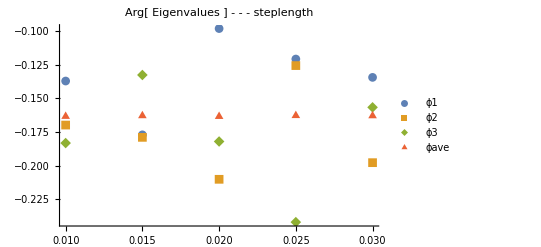

0.162316

```mathematica
bm=Import["Google Drive/jie_programs/QHlattice/steplength/teststeplength_newi3","Table"];
n:=Length[bm]
x=Table[bm[[i]][[1]],{i,1,n,1}];
phase1= Table[{x[[i]],bm[[i]][[2]]},{i,1,n}];
phase2= Table[{x[[i]],bm[[i]][[3]]},{i,1,n}];
phase3= Table[{x[[i]],bm[[i]][[4]]},{i,1,n}];
ave=Table[(bm[[i]][[2]]+bm[[i]][[3]]+bm[[i]][[4]])/3,{i,n}];
phaseave= Table[{x[[i]],ave[[i]]},{i,1,n}];
ϕ1dif= Table[{x[[i]],bm[[i]][[2]]-ave[[i]]},{i,1,n}];
ϕ2dif= Table[{x[[i]],bm[[i]][[3]]-ave[[i]]},{i,1,n}];
ϕ3dif= Table[{x[[i]],bm[[i]][[4]]-ave[[i]]},{i,1,n}];


ListPlot[{phase1,phase2,phase3,phaseave},PlotLegends->{"ϕ1","ϕ2", "ϕ3","ϕave"},PlotMarkers->Automatic, PlotLabel->"Arg[ Eigenvalues ] - - - steplength",PlotRange->{{0.005,0.035},{-0.08,-0.3}}]
31*0.0025*2π/3
```

```mathematica
t=2
bm[[t]]
p1=bm[[t]][[2]];
p2=bm[[t]][[3]];
p3=bm[[t]][[4]];
Arg[Exp[ⅈ p1]+Exp[ⅈ p2]+Exp[ⅈ p3]]
(p1+p2+p3)/3
```

2

{0.025,-0.120876,-0.125729,-0.241983}

-0.162842

-0.162863

```mathematica
Norm[1+ⅈ]
```

√2